Author: Shih-Chen Chao (shih-chen.chao@manchester.ac.uk)
Version 01: 06-November-2018
Version 02: 29-January-2019

# Introduction to Mathematica:

## Part 4: Principles of the Wolfram Language:

1. There are several underlying principles of the Wolfram Language:

## i. All built-in function names are CamelCase: Built-in functions drop-down box, auto-completion, and templates are useful. One click on the Italic [i] blue icon will take you to the documentation page regarding how to use the particular function.

## ii. Expressions to be used inside a built-in function are enclosed by square bracket [ ], divided by “ , “

## iii. Lists (ranges or domains) to be used inside a built-in function are enclosed by curly braces { }, divided by “ , “

## iv. Options are linked using “->”

## v. Shift+Enter to evaluate

## Exercises: find out why the evaluation of the following set of codes is not successful?

```mathematica
Sin[π, 4]
```

Sin::argx: Sin called with 2 arguments; 1 argument is expected.

Sin[π,4]

```mathematica
Mean[1, 3, 5, 7]
```

Mean::argx: Mean called with 4 arguments; 1 argument is expected.

Mean[1,3,5,7]

```mathematica
Total[{1, 4, 8, 13, 19,]
```

```mathematica
InterPolation[{2, 4, 6, 8, 10},3.5](*find an interpolation data at the point of x*)
```

InterPolation[{2,4,6,8,10},3.5]

```mathematica
reverse[{3, 5, 7}]
```

reverse[{3,5,7}]

```mathematica
ToUppercase["Alice fell into a rabbit hole"]
```

ToUppercase[Alice fell into a rabbit hole]

```mathematica
Length["Alice fell into a rabbit hole"](*It is a string!*)
```

0

```mathematica
Table[x-1, {x, 1, 5,}]
```

Table::iterb: Iterator {x,1,5,Null} does not have appropriate bounds.

Table[x-1,{x,1,5,Null}]

```mathematica
ListLinePlot[Range[30]
```

```mathematica
Plot3d[[Sin[xy],{x,-10,10},{y,-5, 5}]]
```

Part::pkspec1: The expression Sin[xy] cannot be used as a part specification.

Plot3d⟦Sin[xy],{x,-10,10},{y,-5,5}⟧

```mathematica
StreanPlot[{-1-x^2+y,1+x-y^2},{x,-10,10},{y,-7,7},mesh->{Range[10]], Filling->Axis]
```

## Part 5: More on data manipulation and visualisation with Mathematica

1. Strings:

i. Use the built-in functions to create, display, and operate on characters, strings and texts.

```mathematica
Alphabet["Arabic"]
```

{ا,ب,ت,ث,ج,ح,خ,د,ذ,ر,ز,س,ش,ص,ض,ط,ظ,ع,غ,ف,ق,ك,ل,م,ن,ه,و,ي}

```mathematica
cRange=CharacterRange["a", "z"]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

Now let’s try some string manipulation. There are a large number of string/text manipulation built-in functions in Mathematica.

```mathematica
sa="It is windy today. "
sb="Winnie the Pooh decides to take a walk."
```

It is windy today.

Winnie the Pooh decides to take a walk.

```mathematica
wPooh=StringJoin[sa, sb]
wPooh=sa<>sb(* <> is a shorthand for StringJoin[]*)
```

It is windy today. Winnie the Pooh decides to take a walk.

It is windy today. Winnie the Pooh decides to take a walk.

```mathematica
Length[wPooh](*why does this built-in funciton not work?*)
```

0

```mathematica
StringLength[wPooh]
```

58

```mathematica
Length[TextWords[wPooh]]
```

12

```mathematica
WordCounts[wPooh]
```

<|walk→1,a→1,take→1,to→1,decides→1,Pooh→1,the→1,Winnie→1,today→1,windy→1,is→1,It→1|>

```mathematica
CharacterCounts[wPooh]
```

<| →11,e→5,i→5,t→5,a→4,o→4,d→4,n→3,k→2,h→2,.→2,y→2,w→2,s→2,l→1,c→1,P→1,W→1,I→1|>

```mathematica
DeleteStopwords[wPooh]
```

windy today. Winnie  Pooh decides    walk.

```mathematica
a="123"
```

123

```mathematica
StringQ[a]
```

True

```mathematica
a=.
```

Let’s try a larger text by using a built-in function to import information of a selected entry from Wikipedia. The evaluated is too long to show everything in the notebook. Therefore we use ‘;’ to suppress the outcome.

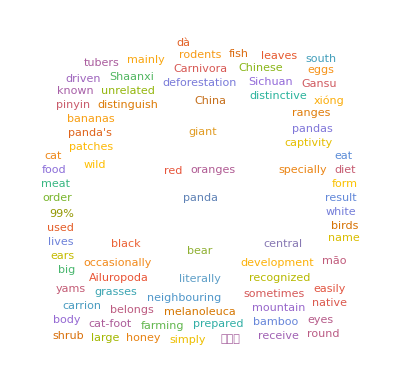

```mathematica
pandaData=WikipediaData["panda"];(* ";" is to repress the outcome*)
WordCloud[DeleteStopwords[StringTake[pandaData, 1000]]]
```

## Question: modify the previous code to make a word cloud of the first 1000 words from Wikipedia article on panda NOT including stopwords

## Answer:

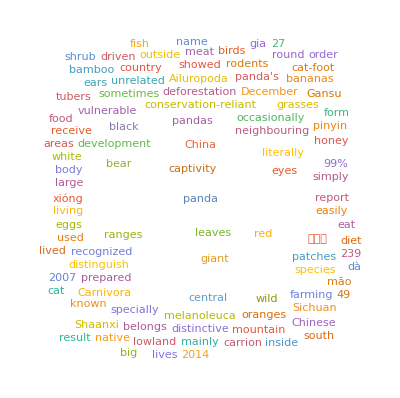

```mathematica
pandaData=WikipediaData["panda"];
WordCloud[StringTake[DeleteStopwords[pandaData],1000]]
```

2. Lists (numerical data):

#### i. Lists (for vectors): lists are a basic way to collect the input data (hereafter “elements”)

<1>. In a list, the elements do not necessarily have to be of the same element type, it can be a set of numbers, a string , an image, even other lists. Unlike some other programming languages, the Wolfram Language does not automatically convert the elements in a list into the same type:

The following list has a mixed dataset of numbers, a string, an image, and two Boolean expressions.

```mathematica
vec1={1, π,"panda", Import["https://www.pandasinternational.org/wptemp/wp-content/uploads/2012/10/slider1.jpg"], Boole[True], Sin[3]<Cos[2]}
```

{1,π,panda,-Graphics-,1,False}

```mathematica
Clear[vec1]
```

<2>. However most of the time, we deal with a list (a vector) of the same element type. Table[ ] and Range[ ] are two of the most useful built-in function to create lists, vectors, matrices, tensors, etc.

Let’s re-visit what we just learned regarding using built-in functions to generate a list (a vector). Notice that we introduce a new function here called Array [].

```mathematica
vec1=Table[x+1, {x, 1, 5}]
vec2=Table[5, 5]
vec3=Range[6, 10]
vec4=Range[1, 10, 2]
vec5=RandomInteger[10, 5]
```

{2,3,4,5,6}

{5,5,5,5,5}

{6,7,8,9,10}

{1,3,5,7,9}

{7,0,2,1,8}

We can perform vector calculation, such as:

```mathematica
vec1+vec3
vec4*vec5
```

{8,10,12,14,16}

{7,0,10,7,72}

<3>. In addition to vector calculation, we can perform operations on lists, such as extracting various parts out of a list.

We can use different built-in functions to manipulate a vector:

```mathematica
Length[vec1]
First[vec1]
Last[vec1]
Take[vec3, 3]
Drop[vec3, 3]
Delete[vec3, 3]
Prepend[vec1, 0]
Append[vec1, 0]
Part[vec3, 4]
vec3[[4]]
Select[vec1, EvenQ]
```

5

2

6

{6,7,8}

{9,10}

{6,7,9,10}

{0,2,3,4,5,6}

{2,3,4,5,6,0}

9

9

{2,4,6}

Part is such a convenient and frequently used built-in function that it has its own shorthand [[ ]].

Question: what is the outcome of vec1[[0]]? What does this tell us about the index in the Wolfram Language?

```mathematica
Length[vec1]
```

5

```mathematica
vec1[[1]]
```

2

<4>. We can visualise the data from the previous outcome. We will re-visit data visualisation later.

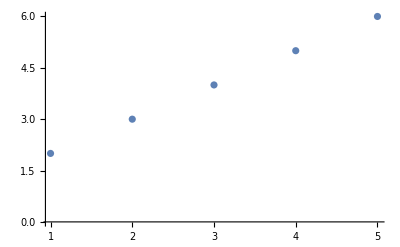
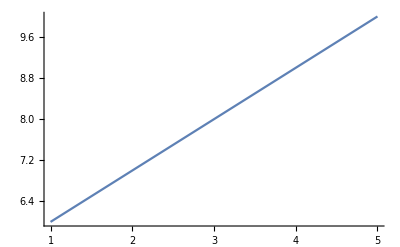
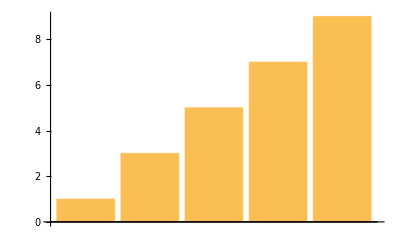
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{ListPlot [vec1, PlotRange->All], ListLinePlot[vec3, PlotRange->All], BarChart[vec4], PieChart[vec5]}
```

```mathematica
Clear[vec1, vec2, vec3, vec4, vec5]
```

#### ii. Lists of lists (for matrices and tensors):

<1>. Create lists of lists and display them:

We can manually create a 2D matrix or use Table [ ] to create a matrix. Notice that we start using two different shorthands to represent [ ]. @ is a prefix whereas // is a postfix.

```mathematica
mat1=Table[x+y, {x, 1, 5}, {y, 1, 5}];
mat1//MatrixForm
mat2=Table[x y, {x, 1, 5}, {y, 1,5}];
TableForm@mat2
```

(2 | 3 | 4 | 5 | 6
3 | 4 | 5 | 6 | 7
4 | 5 | 6 | 7 | 8
5 | 6 | 7 | 8 | 9
6 | 7 | 8 | 9 | 10)

1 | 2 | 3 | 4 | 5
2 | 4 | 6 | 8 | 10
3 | 6 | 9 | 12 | 15
4 | 8 | 12 | 16 | 20
5 | 10 | 15 | 20 | 25

### <2>. Matrix operation:

We can perform  different matrix operation, such as element-wise calculation, dot product and matrix transpose:

```mathematica
mat1+mat2
mat1^mat2
mat1*mat2
dotProduct=mat1. mat2 (*Matrix product: {{a,b},{c,d}} . {{r,s},{t,u}}= {{a r+b t,a s+b u},{c r+d t,c s+d u}}*)
```

{{3,5,7,9,11},{5,8,11,14,17},{7,11,15,19,23},{9,14,19,24,29},{11,17,23,29,35}}

{{2,9,64,625,7776},{9,256,15625,1679616,282475249},{64,15625,10077696,13841287201,35184372088832},{625,1679616,13841287201,281474976710656,12157665459056928801},{7776,282475249,35184372088832,12157665459056928801,10000000000000000000000000}}

{{2,6,12,20,30},{6,16,30,48,70},{12,30,54,84,120},{20,48,84,128,180},{30,70,120,180,250}}

{{70,140,210,280,350},{85,170,255,340,425},{100,200,300,400,500},{115,230,345,460,575},{130,260,390,520,650}}

```mathematica
mat3=Transpose[dotProduct]
mat3//TableForm
```

{{70,85,100,115,130},{140,170,200,230,260},{210,255,300,345,390},{280,340,400,460,520},{350,425,500,575,650}}

70 | 85 | 100 | 115 | 130
140 | 170 | 200 | 230 | 260
210 | 255 | 300 | 345 | 390
280 | 340 | 400 | 460 | 520
350 | 425 | 500 | 575 | 650

### <3>. Matrix extraction:

Like a vector, we can dice a matrix to extract the part we need. In Wolfram Mathematica, ‘ n;;m ‘ means from number ‘n’ to number ‘m’ in matrix operation. We use mat3 as the example.

```mathematica
mat3//MatrixForm
```

(70 | 85 | 100 | 115 | 130
140 | 170 | 200 | 230 | 260
210 | 255 | 300 | 345 | 390
280 | 340 | 400 | 460 | 520
350 | 425 | 500 | 575 | 650)

```mathematica
mat3[[All, 2]]
mat3[[2, All]]
```

{85,170,255,340,425}

{140,170,200,230,260}

```mathematica
mat3[[2, 2]]
```

170

```mathematica
mat3[[2;;5, 1;;3]]//MatrixForm
```

(140 | 170 | 200
210 | 255 | 300
280 | 340 | 400
350 | 425 | 500)

```mathematica
mat3[[1;;5;;2, All]]//MatrixForm
```

(70 | 85 | 100 | 115 | 130
210 | 255 | 300 | 345 | 390
350 | 425 | 500 | 575 | 650)

```mathematica
mat3[[1;;5;;2, 1;;5;;3]]//MatrixForm
```

(70 | 115
210 | 345
350 | 575)

```mathematica
mat1
```

{{2,3,4,5,6},{3,4,5,6,7},{4,5,6,7,8},{5,6,7,8,9},{6,7,8,9,10}}

```mathematica
mat2
```

{{1,2,3,4,5},{2,4,6,8,10},{3,6,9,12,15},{4,8,12,16,20},{5,10,15,20,25}}

```mathematica
mat3
```

{{70,85,100,115,130},{140,170,200,230,260},{210,255,300,345,390},{280,340,400,460,520},{350,425,500,575,650}}

```mathematica
Part[mat1, 3]
```

{4,5,6,7,8}

It goes the same with vector manipulation that there are a large number of built-in functions we can use to manipulate matrices and arrays. Discuss with your neighbor what the outcome is.

```mathematica
Length[mat1]
Dimensions[mat1]
Take[mat1, 2]
Drop[mat1, -1]
Delete[mat1,3]
ReplacePart[mat1, 5->5]
Select[Flatten[mat3], #<100&]
(*Table[Select[mat3[[All, i]], #<200&], {i, 1, Length[mat3]}]*)
(*Table[Select[mat3[[i, All]], #<150&], {i, 1, Length[mat3]}]*)
```

5

{5,5}

{{2,3,4,5,6},{3,4,5,6,7}}

{{2,3,4,5,6},{3,4,5,6,7},{4,5,6,7,8},{5,6,7,8,9}}

{{2,3,4,5,6},{3,4,5,6,7},{5,6,7,8,9},{6,7,8,9,10}}

{{2,3,4,5,6},{3,4,5,6,7},{4,5,6,7,8},{5,6,7,8,9},5}

{70,85}

3. Data import and visualisation: Serial killers

Apart from data generation using built-in functions or relying on user to perform direct input, we also import data to perform various tasks.

i. Set the directory where the data is.

```mathematica
SetDirectory["/home/Pooh_Centos/Desktop/IntroMM_Jan2019"];
Directory[]
Column[FileNames[]]
cmap=ColorData[64]
```

/home/Pooh_Centos/Desktop/IntroMM_Jan2019

.git
LazyPanda.jpg
MathematicaTeachingMaterial_FullVersion02.nb
MM1_5.nb
MM6_9.nb
model.dae
README.md
ScriptLoad.wls
SerialKiller_byCountry.csv
SerialKiller_byYear.csv
SerialKillerVictims_byAge.csv
TestPackage.m

ColorDataFunction[…]

(*importSheets=Import["SerialKiller_Data.xlsx", "Sheets"]*)
(*Import["SerialKiller_Data.xlsx", {"Data", "SerialKiller_byCountry_2018"}, HeaderLines→1]*)

## ii. Serial killers across the globe, 1900 - 2018:

### <1>. Data manipulation:

```mathematica
skbyCountry=Import["SerialKiller_byCountry.csv", "Data", HeaderLines->1]
Dimensions[skbyCountry]
```

{{USA-UnitedStates,1948},{GBR-UnitedKingdom,131},{ZAF-SouthAfrica,94},{ITA-Italy,93},{DEU-Germany,78},{CAN-Canada,69},{AUS-Australia,55},{FRA-France,53},{JPN-Japan,40},{IND-India,39},{RUS-Russia,37},{CHN-China,30},{MEX-Mexico,24},{AUT-Austria,18},{BRA-Brazil,14},{ANT-Netherlands,11},{ESP-Spain,11},{POL-Poland,10},{IRN-Iran,8},{COL-Colombia,7},{BEL-Belgium,7},{THA-Thailand,6},{KOR-SouthKorea,5},{SWE-Sweden,5},{CHE-Switzerland,5},{GRC-Greece,5},{PAK-Pakistan,5},{KEN-Kenya,5},{SGP-Singapore,4},{PHL-Philippines,4},{HUN-Hungary,4},{IDN-Indonesia,4},{ISR-Israel,4},{VNM-Vietnam,4},{CZE-CzechRepublic,4},{HKG-HongKong,3},{YEM-Yemen,3},{UGA-Uganda,3},{BMU-Bermuda,3},{TUR-Turkey,3},{NZL-NewZealand,3},{FIN-Finland,3},{MKD-Macedonia,3},{ROM-Romania,3},{SWZ-Swaziland,3},{ZWE-Zimbabwe,2},{MAR-Morocco,2},{ECU-Ecuador,2},{NOR-Norway,2},{GTM-Guatemala,2},{BHS-Bahamas,2},{ARG-Argentina,2},{PAN-Panama,2},{IRL-Ireland,2},{JOR-Jordan,2},{EGY-Egypt,2},{YUG-Yugoslavia,2},{SVN-Slovenia,2},{URY-Uruguay,2},{ATG-Antigua,1},{AGO-Angola,1},{NGA-Nigeria,1},{SAU-SaudiArabia,1},{BOL-Bolivia,1},{PER-Peru,1},{SVK-Slovakia,1},{PRT-Portugal,1},{CostaRica,1},{BGD-Bangladesh,1},{MLT-Malta,1},{SYR-SyrianArabRepublic,1},{BLR-Belarus,1},{SLV-ElSalvador,1},{UAE-UnitedArabEmirates,1},{DNK-Denmark,1},{LVA-RepublicofLatvia,1},{HRV-RepublicofCroatia,1},{GHA-Ghana,1},{HOL-Holland,1},{EST-Estonia,1},{AFG-Afghanistan,1},{NPL-Nepal,1},{VEN-Venezuela,1},{MDA-Moldova,1},{KGZ-Kyrgyzstan,1},{FJI-Fiji,1},{Gaul,1},{KAZ-Kazakhstan,1},{BIH-Bosnia,1},{BWA-Botswana,1}}

{90,2}

```mathematica
skbyCountryAssoc=Association[Table[skbyCountry[[i, 1]]->skbyCountry[[i, 2]], {i, 1, Length[skbyCountry]}]]
```

<|USA-UnitedStates→1948,GBR-UnitedKingdom→131,ZAF-SouthAfrica→94,ITA-Italy→93,DEU-Germany→78,CAN-Canada→69,AUS-Australia→55,FRA-France→53,JPN-Japan→40,IND-India→39,RUS-Russia→37,CHN-China→30,MEX-Mexico→24,AUT-Austria→18,BRA-Brazil→14,ANT-Netherlands→11,ESP-Spain→11,POL-Poland→10,IRN-Iran→8,COL-Colombia→7,BEL-Belgium→7,THA-Thailand→6,KOR-SouthKorea→5,SWE-Sweden→5,CHE-Switzerland→5,GRC-Greece→5,PAK-Pakistan→5,KEN-Kenya→5,SGP-Singapore→4,PHL-Philippines→4,HUN-Hungary→4,IDN-Indonesia→4,ISR-Israel→4,VNM-Vietnam→4,CZE-CzechRepublic→4,HKG-HongKong→3,YEM-Yemen→3,UGA-Uganda→3,BMU-Bermuda→3,TUR-Turkey→3,NZL-NewZealand→3,FIN-Finland→3,MKD-Macedonia→3,ROM-Romania→3,SWZ-Swaziland→3,ZWE-Zimbabwe→2,MAR-Morocco→2,ECU-Ecuador→2,NOR-Norway→2,GTM-Guatemala→2,BHS-Bahamas→2,ARG-Argentina→2,PAN-Panama→2,IRL-Ireland→2,JOR-Jordan→2,EGY-Egypt→2,YUG-Yugoslavia→2,SVN-Slovenia→2,URY-Uruguay→2,ATG-Antigua→1,AGO-Angola→1,NGA-Nigeria→1,SAU-SaudiArabia→1,BOL-Bolivia→1,PER-Peru→1,SVK-Slovakia→1,PRT-Portugal→1,CostaRica→1,BGD-Bangladesh→1,MLT-Malta→1,SYR-SyrianArabRepublic→1,BLR-Belarus→1,SLV-ElSalvador→1,UAE-UnitedArabEmirates→1,DNK-Denmark→1,LVA-RepublicofLatvia→1,HRV-RepublicofCroatia→1,GHA-Ghana→1,HOL-Holland→1,EST-Estonia→1,AFG-Afghanistan→1,NPL-Nepal→1,VEN-Venezuela→1,MDA-Moldova→1,KGZ-Kyrgyzstan→1,FJI-Fiji→1,Gaul→1,KAZ-Kazakhstan→1,BIH-Bosnia→1,BWA-Botswana→1|>

### <2>. Data visualisation:

When we visualise data, various plot built-in functions are available. It is convenient to use Option[ ] to make query of what options are available.

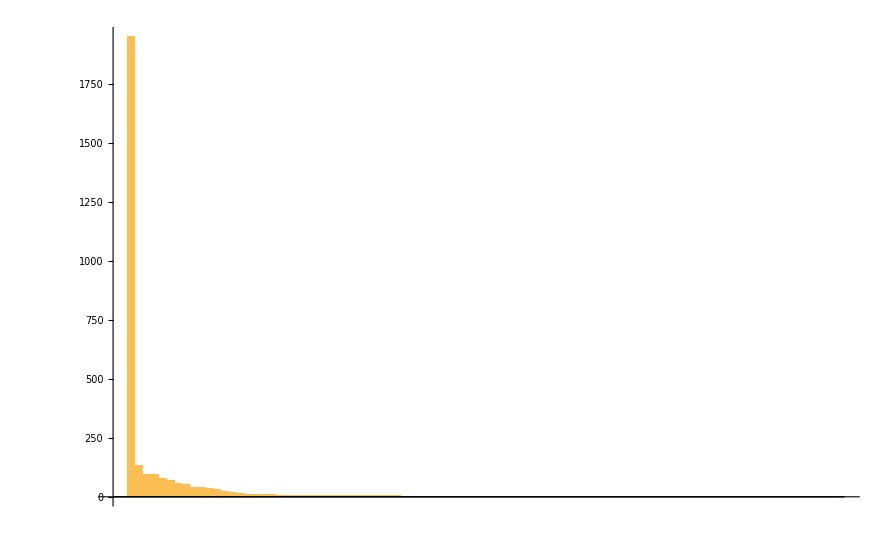

```mathematica
BarChart[Values[skbyCountryAssoc]]
```

```mathematica
Options[BarChart]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→Automatic,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BarOrigin→Bottom,BarSpacing→Automatic,BaselinePosition→Automatic,BaseStyle→{},ChartBaseStyle→Automatic,ChartElementFunction→Automatic,ChartElements→Automatic,ChartLabels→None,ChartLayout→Automatic,ChartLegends→None,ChartStyle→Automatic,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,Joined→False,LabelingFunction→Automatic,LabelingSize→Automatic,LabelStyle→{},LegendAppearance→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotRange→All,PlotRangeClipping→False,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{}}

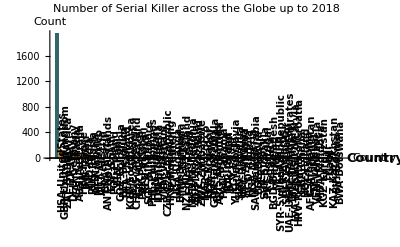

```mathematica
BarChart[Values[skbyCountryAssoc],ChartLabels->Placed[Keys[skbyCountryAssoc], Below, Rotate[Style[#,10, Bold],Pi/2]&], ChartStyle->cmap, PlotLabel->Style["Number of Serial Killer across the Globe up to 2018", Purple, 20, Bold], AxesLabel->{Style["Country", 13, Bold], Style["Count", 13, Bold]}]
```

## iii. Heat map of serial killer countries, 1900-2018:

### <1>. Data manipulation:

```mathematica
cLabel=skbyCountry[[All, 1]]
sknCountry=skbyCountry[[All, 2]]
```

{USA-UnitedStates,GBR-UnitedKingdom,ZAF-SouthAfrica,ITA-Italy,DEU-Germany,CAN-Canada,AUS-Australia,FRA-France,JPN-Japan,IND-India,RUS-Russia,CHN-China,MEX-Mexico,AUT-Austria,BRA-Brazil,ANT-Netherlands,ESP-Spain,POL-Poland,IRN-Iran,COL-Colombia,BEL-Belgium,THA-Thailand,KOR-SouthKorea,SWE-Sweden,CHE-Switzerland,GRC-Greece,PAK-Pakistan,KEN-Kenya,SGP-Singapore,PHL-Philippines,HUN-Hungary,IDN-Indonesia,ISR-Israel,VNM-Vietnam,CZE-CzechRepublic,HKG-HongKong,YEM-Yemen,UGA-Uganda,BMU-Bermuda,TUR-Turkey,NZL-NewZealand,FIN-Finland,MKD-Macedonia,ROM-Romania,SWZ-Swaziland,ZWE-Zimbabwe,MAR-Morocco,ECU-Ecuador,NOR-Norway,GTM-Guatemala,BHS-Bahamas,ARG-Argentina,PAN-Panama,IRL-Ireland,JOR-Jordan,EGY-Egypt,YUG-Yugoslavia,SVN-Slovenia,URY-Uruguay,ATG-Antigua,AGO-Angola,NGA-Nigeria,SAU-SaudiArabia,BOL-Bolivia,PER-Peru,SVK-Slovakia,PRT-Portugal,CostaRica,BGD-Bangladesh,MLT-Malta,SYR-SyrianArabRepublic,BLR-Belarus,SLV-ElSalvador,UAE-UnitedArabEmirates,DNK-Denmark,LVA-RepublicofLatvia,HRV-RepublicofCroatia,GHA-Ghana,HOL-Holland,EST-Estonia,AFG-Afghanistan,NPL-Nepal,VEN-Venezuela,MDA-Moldova,KGZ-Kyrgyzstan,FJI-Fiji,Gaul,KAZ-Kazakhstan,BIH-Bosnia,BWA-Botswana}

{1948,131,94,93,78,69,55,53,40,39,37,30,24,18,14,11,11,10,8,7,7,6,5,5,5,5,5,5,4,4,4,4,4,4,4,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
(*sample30=Keys[skbyCountryAssoc][[1;;30]]*)
sample30=cLabel[[1;;30]]
Dimensions[sample30]
sample30[[1]]
StringQ[sample30[[3]]]
top30Country=Table[StringJoin[Drop[Characters[sample30[[i]]], 4]], {i, 1, Length[sample30]}]
```

{USA-UnitedStates,GBR-UnitedKingdom,ZAF-SouthAfrica,ITA-Italy,DEU-Germany,CAN-Canada,AUS-Australia,FRA-France,JPN-Japan,IND-India,RUS-Russia,CHN-China,MEX-Mexico,AUT-Austria,BRA-Brazil,ANT-Netherlands,ESP-Spain,POL-Poland,IRN-Iran,COL-Colombia,BEL-Belgium,THA-Thailand,KOR-SouthKorea,SWE-Sweden,CHE-Switzerland,GRC-Greece,PAK-Pakistan,KEN-Kenya,SGP-Singapore,PHL-Philippines}

{30}

USA-UnitedStates

True

{UnitedStates,UnitedKingdom,SouthAfrica,Italy,Germany,Canada,Australia,France,Japan,India,Russia,China,Mexico,Austria,Brazil,Netherlands,Spain,Poland,Iran,Colombia,Belgium,Thailand,SouthKorea,Sweden,Switzerland,Greece,Pakistan,Kenya,Singapore,Philippines}

```mathematica
geoDataGlobe=Table[Entity["Country", top30Country[[i]]]->sknCountry[[i]], {i, 1, 30}]
Dimensions[geoDataGlobe]
```

{United States→1948,United Kingdom→131,South Africa→94,Italy→93,Germany→78,Canada→69,Australia→55,France→53,Japan→40,India→39,Russia→37,China→30,Mexico→24,Austria→18,Brazil→14,Netherlands→11,Spain→11,Poland→10,Iran→8,Colombia→7,Belgium→7,Thailand→6,South Korea→5,Sweden→5,Switzerland→5,Greece→5,Pakistan→5,Kenya→5,Singapore→4,Philippines→4}

{30}

### <2>. Data visualisation:

```mathematica
heatMapSKbyCountry=GeoRegionValuePlot[geoDataGlobe, ColorFunctionScaling->True, GeoLabels->True, LabelStyle->{5, Bold, Italic, Purple}]
```

-Graphics-

The default setting of the map is way too small. We can manually change the size, or check what type of options we have to make the map larger.

```mathematica
Options[GeoRegionValuePlot]
```

{AlignmentPoint→Center,AspectRatio→Automatic,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→Automatic,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ColorRules→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GeoBackground→Automatic,GeoCenter→Automatic,GeoGridLines→None,GeoGridLinesStyle→Automatic,GeoLabels→None,GeoModel→Automatic,GeoProjection→Automatic,GeoRange→Automatic,GeoRangePadding→Automatic,GeoScaleBar→None,GeoServer→Automatic,GeoZoomLevel→Automatic,GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→Automatic,Method→Automatic,MissingStyle→Automatic,PlotLabel→None,PlotLegends→Automatic,PlotMarkers→Automatic,PlotRange→All,PlotRangeClipping→False,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{}}

Question: add the option of ‘ImageSize->All’ to the code to see what happens after the re-evaluation?

## iv. Number and age of victims by serial killing in the US, 1900 - 2014:

### <1>. Data Manipulation:

```mathematica
skvAge=Import["SerialKillerVictims_byAge.csv", HeaderLines->1]
skvAgeAssoc=Association[Table[skvAge[[i, 1]]->skvAge[[i, 2]], {i, 1, Length[skvAge]}]]
```

{{0,137},{1,42},{2,47},{3,46},{4,48},{5,40},{6,47},{7,49},{8,55},{9,75},{10,63},{11,62},{12,92},{13,106},{14,142},{15,192},{16,212},{17,242},{18,290},{19,312},{20,266},{21,287},{22,293},{23,232},{24,248},{25,226},{26,228},{27,221},{28,180},{29,212},{30,192},{31,156},{32,154},{33,136},{34,158},{35,158},{36,137},{37,129},{38,135},{39,121},{40,123},{41,105},{42,118},{43,95},{44,95},{45,102},{46,79},{47,77},{48,81},{49,69},{50,92},{51,67},{52,74},{53,63},{54,53},{55,57},{56,60},{57,56},{58,55},{59,53},{60,66},{61,43},{62,64},{63,42},{64,48},{65,56},{66,39},{67,42},{68,48},{69,52},{70,30},{71,29},{72,46},{73,38},{74,32},{75,38},{76,32},{77,26},{78,31},{79,37},{80,36},{81,40},{82,32},{83,31},{84,19},{85,28},{86,23},{87,23},{88,12},{89,13},{90,14},{91,11},{92,4},{93,3},{94,3},{95,3},{96,0},{97,2},{98,2},{99,1},{100,1}}

<|0→137,1→42,2→47,3→46,4→48,5→40,6→47,7→49,8→55,9→75,10→63,11→62,12→92,13→106,14→142,15→192,16→212,17→242,18→290,19→312,20→266,21→287,22→293,23→232,24→248,25→226,26→228,27→221,28→180,29→212,30→192,31→156,32→154,33→136,34→158,35→158,36→137,37→129,38→135,39→121,40→123,41→105,42→118,43→95,44→95,45→102,46→79,47→77,48→81,49→69,50→92,51→67,52→74,53→63,54→53,55→57,56→60,57→56,58→55,59→53,60→66,61→43,62→64,63→42,64→48,65→56,66→39,67→42,68→48,69→52,70→30,71→29,72→46,73→38,74→32,75→38,76→32,77→26,78→31,79→37,80→36,81→40,82→32,83→31,84→19,85→28,86→23,87→23,88→12,89→13,90→14,91→11,92→4,93→3,94→3,95→3,96→0,97→2,98→2,99→1,100→1|>

### <2>. Data Visualisation:

```mathematica
(*BarChart[Labeled[#,Style[#, 10],Above]&/@Values[skvAgeAssoc], ChartLabels->Placed[Keys[skvAgeAssoc], Below, Rotate[Style[#,12, Bold],Pi/2]&],BarSpacing->Large, AxesLabel->{Style["Age of Victims", Red, Bold], Style["Number of Victims", Red, Bold]}, ChartStyle->cmap]*)
```

```mathematica
(*ListLinePlot[Table[Values[skvAgeAssoc][[i]], {i, 1, Length[skvAgeAssoc]}], AxesLabel->{Style["Age of Victims", Red, Bold], Style["Number of Victims", Red, Bold]}, PlotMarkers->Automatic, PlotLabel->Style["Number of Serial Killer Victims in the US, 1900-2014", Purple, 20, Bold], ImageSize->Large]*)
```

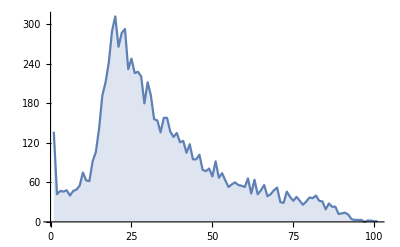

```mathematica
StackedListPlot[Table[Values[skvAgeAssoc][[i]], {i, 1, Length[skvAgeAssoc]}]]
```

```mathematica
Options[StackedListPlot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Filling→Automatic,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,InterpolationOrder→None,Joined→True,LabelingFunction→Automatic,LabelingSize→Automatic,LabelStyle→{},MaxPlotPoints→∞,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLayout→Stacked,PlotLegends→None,PlotMarkers→None,PlotRange→All,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{}}

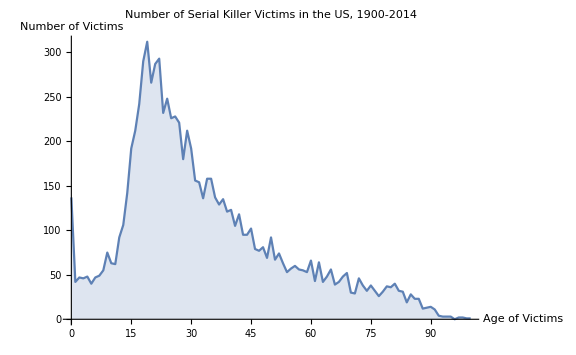

```mathematica
StackedListPlot[Table[{Keys[skvAgeAssoc][[i]], Values[skvAgeAssoc][[i]]}, {i, 1, Length[skvAgeAssoc]}], AxesLabel->{Style["Age of Victims", Red, Bold], Style["Number of Victims", Red, Bold]}, PlotLabel->Style["Number of Serial Killer Victims in the US, 1900-2014", Purple, 20, Bold], ImageSize->Large]
```

## Exercise: plot the SerialKiller_byYear data showing stacked data and the corresponding date.

#### 1. Import the dataset (use Directory [] to double check your current directory) and remember to remove the headerline 2. Use StackedListDatePlot [] to plot the data. 3. Go to Help page to work out which column of data from the imported csv would need to be extracted. 4. Copy and paste the example from the help page to the notebook and modify the data to make sure the example works 5. Use StackedListDatePlot to plot the two sets of data of ‘2 or more victims’ and ‘3 or more victims’ over the year from 1920 to 2014. 6. Check what options StackedListDatePlot [] takes to provide more information to the plot.

## Answer:

```mathematica
Directory[]
```

/home/Pooh_Centos/Desktop/IntroMM_Jan2019

```mathematica
"/home/Pooh_Centos/Desktop/IntroMM_Jan2019"
```

/home/Pooh_Centos/Desktop/IntroMM_Jan2019

```mathematica
skvbyYear=Import["/home/Pooh_Centos/Desktop/MTM_Revised/SerialKiller_byYear.csv", HeaderLines->1]
```

{{1920,13,13},{1921,17,14},{1922,8,8},{1923,17,14},{1924,6,6},{1925,9,9},{1926,11,7},{1927,9,8},{1928,9,9},{1929,5,5},{1930,6,5},{1931,10,8},{1932,11,10},{1933,12,10},{1934,8,7},{1935,11,12},{1936,8,8},{1937,8,9},{1938,9,10},{1939,6,6},{1940,6,6},{1941,3,3},{1942,4,0},{1943,8,8},{1944,8,9},{1945,11,9},{1946,12,10},{1947,5,6},{1948,9,7},{1949,5,6},{1950,10,8},{1951,12,10},{1952,7,7},{1953,9,8},{1954,13,10},{1955,9,8},{1956,13,11},{1957,14,9},{1958,15,14},{1959,7,6},{1960,18,11},{1961,15,11},{1962,13,9},{1963,21,16},{1964,29,16},{1965,21,12},{1966,36,27},{1967,24,20},{1968,31,22},{1969,43,39},{1970,42,34},{1971,55,41},{1972,68,52},{1973,76,58},{1974,99,71},{1975,92,61},{1976,84,51},{1977,105,71},{1978,131,83},{1979,117,88},{1980,124,90},{1981,134,99},{1982,113,83},{1983,114,81},{1984,142,94},{1985,148,104},{1986,159,106},{1987,172,119},{1988,138,78},{1989,152,100},{1990,129,85},{1991,146,85},{1992,151,101},{1993,153,91},{1994,142,92},{1995,126,71},{1996,124,72},{1997,111,74},{1998,116,76},{1999,102,60},{2000,83,54},{2001,85,50},{2002,88,54},{2003,82,57},{2004,74,48},{2005,74,56},{2006,75,53},{2007,84,56},{2008,60,34},{2009,76,42},{2010,61,29},{2011,56,25},{2012,55,17},{2013,29,15},{2014,25,13}}

```mathematica
skyYear2v=skvbyYear[[All, 2]]
```

{13,17,8,17,6,9,11,9,9,5,6,10,11,12,8,11,8,8,9,6,6,3,4,8,8,11,12,5,9,5,10,12,7,9,13,9,13,14,15,7,18,15,13,21,29,21,36,24,31,43,42,55,68,76,99,92,84,105,131,117,124,134,113,114,142,148,159,172,138,152,129,146,151,153,142,126,124,111,116,102,83,85,88,82,74,74,75,84,60,76,61,56,55,29,25}

```mathematica
skyYear3v=skvbyYear[[All, 3]]
```

{13,14,8,14,6,9,7,8,9,5,5,8,10,10,7,12,8,9,10,6,6,3,0,8,9,9,10,6,7,6,8,10,7,8,10,8,11,9,14,6,11,11,9,16,16,12,27,20,22,39,34,41,52,58,71,61,51,71,83,88,90,99,83,81,94,104,106,119,78,100,85,85,101,91,92,71,72,74,76,60,54,50,54,57,48,56,53,56,34,42,29,25,17,15,13}

```mathematica
data1=TimeSeries[skyYear2v, {"1920", "2014"}];
data2=TimeSeries[skyYear3v, {"1920", "2014"}];
```

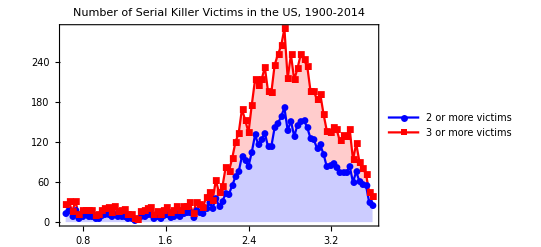

-Graphics-

```mathematica
StackedDateListPlot[{data1,data2}, PlotStyle-> {Directive[Blue], Directive[Red]}, PlotLegends->{"2 or more victims", "3 or more victims"},   PlotLabel->Style["Number of Serial Killer Victims in the US, 1900-2014", Purple, 20, Bold], PlotMarkers->Automatic](*No AxeLabel option for this plotting*)
```

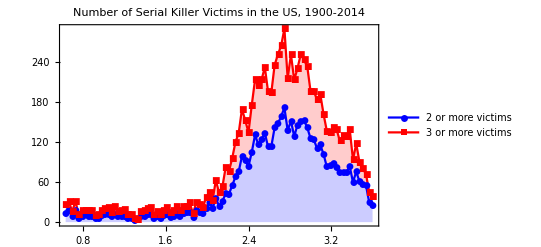

```mathematica
StackedDateListPlot[{skyYear2v, skyYear3v}, {1920},PlotStyle-> {Directive[Blue], Directive[Red]}, PlotLegends->{"2 or more victims", "3 or more victims"},   PlotLabel->Style["Number of Serial Killer Victims in the US, 1900-2014", Purple, 20, Bold], PlotMarkers->Automatic]
```

### vi. For Your Reference: a summary of keyboard shortcuts, shorthands, and operators which have been introduced so far.

<1>. Free Form Query | Press =(equal sign) once 
Wolfram Alpha Qurey  |  Press =(equal sign) twice 

<2>. Pi (π) | [Esc]-> p-> [Esc] in sequence or [Esc p] together to bring out the drop-down list to choose from   

<3>. Exponentiation  | x^y | x→[Ctrl+^ or Ctrl +6]→ y
Root | x^(1/y) | [Ctrl +2] →x,  [Ctrl +5]→y
Fraction  | x/y | x→ [Ctrl+/]→y  

<4>. % | The last output (it is the last cell you evaluate,not necessarily the cell immediately preceding the cell you are about to evaluate next.
%37 | The result of the 37^th output, but once the cell number changes, the notebook does not update automatically
Out[37] | The result of the 37^th output,you can see which input and output are which as it is shown on the far left side of each cell.
In[37] | The 37^th input  
  
<5>. [[ ]] | Shorthand for Part[[ ]], very useful
// | Postfix Shorthand for [ ] (i.e. Total[{1, 2, 3}] can be written as {1, 2, 3}//Total)
@ | Pretfix Shorthand for [ ] (i.e. Total[{1, 2, 3}] can be written as Total@{1, 2, 3})
<> | Shorthand for StringJoin[ ].
/@ | Shorthand for Map [].
                    
<6>. ; | Put it at the end of a set of code to suppress the evaluation outcome.
;; | Used to specify the relevant rows and columns to extract part of a list or of a matrix.
&& | Relational operator of 'and'
? | Enquire any built-in function, self-defined function, variables and their assigned value

## Part 6: More on Graphics and using Interactivity

## 1. Graphics: The built-in functions to produce graphics objects are made of three elements, Primitives, Directives, and Options. We can apply these three elements to creating either a static graphic or a dynamic graphic.

### i. A Primitive is a 2D object to create points, lines, polygons, disks, circles. The same notion can be applied to create a 3D object. ii. Directives are used to modify the style, shape, or size of a Primitive. iii. Options are used to give control over the style of the entire plot, such as modifying grid lines, plot frames, background color, aspect ration of the graphic, etc. iv. Wrappers can go around the generated Graphics to add more features to customise your graphics. v. A basic pattern would be: Wrapper[Graphics[{Directives, Primitive}, Options] (Graphics[ ] can be replaced by Graphics3D[ ], which takes 3D Primitive Graphics expressions such as Sphere[ ]and Cylinder[ ]).

Let’s try a 2D example by creating a disk by default, then change the color by adding ‘Directives’ before ‘Primitives’. The two disks will be presented as a list.

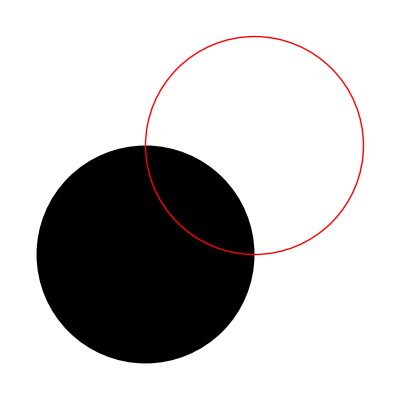

```mathematica
Show[{Graphics[Disk[{1, 1}]], Graphics[{Directive[Red,Thick],Circle[{2, 2}]}]}]
```

Let’s try another 2D example by creating a layer of overlapping regular polygon from a triangle to a hexagon.

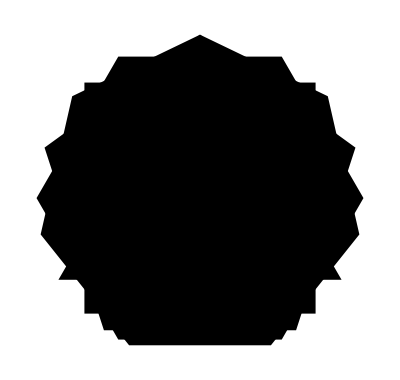

```mathematica
Graphics[Table[RegularPolygon[n], {n, 3, 7}]]
```

Next, let’s add some ‘Directives’ to change the color and some more ‘Options’.

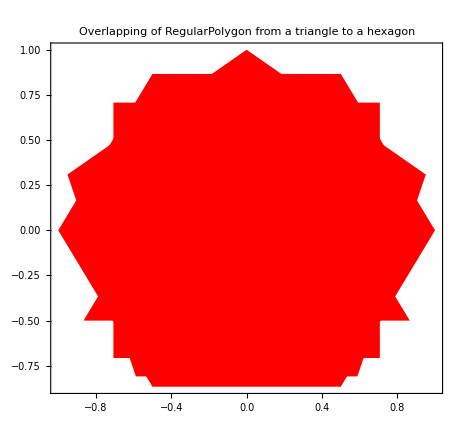

```mathematica
Show[Graphics[{Directive[Red], Table[RegularPolygon[n], {n, 3, 6}]}, PlotLabel->"Overlapping of RegularPolygon from a triangle to a hexagon", Frame->True, FrameStyle->Directive[Red,Dotted]]]
```

We create a list of cylinder, sphere, 4 pointed polygon and put them together in one cubicle space, instead of showing them in a list.

```mathematica
Show[{Graphics3D[Cylinder[{{0, 0, 0},{1, 1, 1}}]], Graphics3D[Sphere[{3, 3, 3}]],Graphics3D[Polygon[{{2, 4, 6},{3, 6, 9},{6, 2,4}, {9, 3, 6}}]]}]
```

-Graphics3D-

Now let’s add more Options.

```mathematica
Show[{Graphics3D[Cylinder[{{0, 0, 0},{1, 1, 1}}]], Graphics3D[Sphere[{3, 3, 3}]],Graphics3D[Polygon[{{2, 4, 6},{3, 6, 9},{6, 2,4}, {9, 3, 6}}]]}, PlotLabel-> "Cylinder, Sphere, and an Irregular Polygon in one cubicle space", LabelStyle->Directive[10, Bold, Red],Axes->True, AspectRatio->Automatic]
```

-Graphics3D-

(Graphics: http://reference.wolfram.com/language/ref/Graphics.html)

## 2. Plots: a quick re-cap about 2D and 3D plotting: we are going to ‘recycle’ the previously-used examples to make them interactive.

Make a plot taking one argument of Sin [x], with x’s range between 0 and 7, using Plot function.

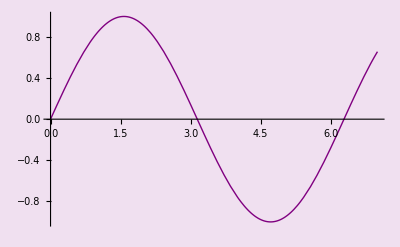

```mathematica
Plot[Sin[x], {x, 0, 7}, Background->LightPurple, PlotStyle->Directive[Purple, Thick]]
```

Make a 3D plot taking 2 arguments of Sin[x]+Cos[y], with both x’s and y’s ranges between 0 and 10, using Plot3D function.

```mathematica
Plot3D[Sin[x]+Cos[y], {x, 0, 10}, {y, 0, 10}, MeshStyle->Dashed, Filling->Axis, PlotLabel->"A 3D Plot", ColorFunction->"Rainbow" ]
```

-Graphics3D-

Let’s try a new example of using SphericalPlot3D[ ]. For the object of Texture[ ], we can drag and drop any image online.

```mathematica
SphericalPlot3D[1+Sin[5 ϕ] Cos [10 θ]/12, {ϕ, 0, π},{θ, 0, 2π}, Axes->False,Mesh->None, Boxed->False, Background->Purple, Lighting->"Neutral", PlotStyle->Texture[-Graphics-]]
```

-Graphics3D-

## 3. Manipulate and Animate: Dynamic Interface for Interactivity :

In Mathematica, Manipulate[ ] is a powerful built-in function to create a dynamic interface by changing and updating any parameter we want. This built-in function takes the form of Manipulate [a set of code, {parameter, a, b}] with the parameter being incorporated inside the set of code we would like to evaluate.  Let’s use the previously-evaluate examples to see the way in which Manipulate[ ] can be applied to them to make those examples dynamic. We can also replace Manipulate[ ] with Animate[ ].

```mathematica
Manipulate[Show[{Graphics[Disk[{1, x}]], Graphics[{Directive[Red,Thick],Circle[{y, 2}]}]}, Frame->True],{x, 0, 10}, {y, 10, 1}]
```

```mathematica
Manipulate[Graphics[{Directive[RandomColor[]], Table[RegularPolygon[n], {n, 3, f}]}, PlotLabel->"Overlapping of RegularPolygon from a triangle to a hexagon", Frame->True, FrameStyle->Directive[Red,Dotted]], {f, 3, 20}]
```

```mathematica
Manipulate[Show[{Graphics3D[Cylinder[{{0, 0, 0},{0.3 a, 0.5 a, 0.7 a}}]], Graphics3D[Sphere[{3, 3, 3}]],Graphics3D[Polygon[{{a, 2 a, 3 a},{3, 6, 9},{3 a, a,2 a}, {9, 3, 6}}]]}, PlotLabel-> "Cylinder, Sphere, and an Irregular Polygon in one cubicle space", LabelStyle->Directive[10, Bold, Red],Axes->Full, Image->Full, AspectRatio->All], {a, 1, 10, 0.01}]
```

```mathematica
Manipulate[Plot[f[x], {x, 10π, -10π},PlotStyle->Directive[Pink, Thick], Background->LightPurple ], {f, {Sin, Cos, Tan, Cot, Sec, Csc}}]
```

```mathematica
Manipulate[Plot3D[m[x y], {x, -7π, 7π}, {y, -7, 7}, Mesh->True, MeshStyle->Automatic, ColorFunction->"Rainbow"], {m, {Sin, Cos, Tan, Cot, Sec, Csc}}]
```

```mathematica
Manipulate[SphericalPlot3D[1+Sin[5 ϕ] Cos [10 θ]/shape, {ϕ, 0, π},{θ, 0, 2π}, Axes->False,Mesh->None, Boxed->False, Background->Purple, Lighting->"Neutral", PlotStyle->Texture[-Graphics-]], {shape,Range[1, 12, 0.5]}]
```

Exercise:
Choose any two examples wrapped by Manipulate [ ] and replace the wrapper with Animate [ ], what happens?

### Answers:

```mathematica
Animate[Show[{Graphics[Disk[{1, x}]], Graphics[{Directive[Red,Thick],Circle[{y, 2}]}]}, Frame->True],{x, 0, 10}, {y, 10, 1}]
```

```mathematica
Animate[Graphics[{Directive[RandomColor[]], Table[RegularPolygon[n], {n, 3, f}]}, PlotLabel->"Overlapping of RegularPolygon from a triangle to a hexagon", Frame->True, FrameStyle->Directive[Red,Dotted]], {f, 3, 20}]
```

```mathematica
Animate[Show[{Graphics3D[Cylinder[{{0, 0, 0},{0.3 a, 0.5 a, 0.7 a}}]], Graphics3D[Sphere[{3, 3, 3}]],Graphics3D[Polygon[{{a, 2 a, 3 a},{3, 6, 9},{3 a, a,2 a}, {9, 3, 6}}]]}, PlotLabel-> "Cylinder, Sphere, and an Irregular Polygon in one cubicle space", LabelStyle->Directive[10, Bold, Red],Axes->Full, Image->Full, AspectRatio->All], {a, 1, 10, 0.01}]
```

```mathematica
Animate[Plot[f[x], {x, 10π, -10π},PlotStyle->Directive[Pink, Thick], Background->LightPurple ], {f, {Sin, Cos, Tan, Cot, Sec, Csc}}]
```

```mathematica
Animate[Plot3D[m[x y], {x, -7π, 7π}, {y, -7, 7}, Mesh->True, MeshStyle->Automatic, ColorFunction->"Rainbow"], {m, {Sin, Cos, Tan, Cot, Sec, Csc}}]
```

```mathematica
Animate[SphericalPlot3D[1+Sin[5 ϕ] Cos [10 θ]/shape, {ϕ, 0, π},{θ, 0, 2π}, Axes->False,Mesh->None, Boxed->False, Background->Purple, Lighting->"Neutral", PlotStyle->Texture[-Graphics-]], {shape,Range[1, 12, 0.5]}]
```

## Part 7: More to the Wolfram Mathematica Language: self-defined function

1. Function Definitions:

### It would seem that with the numerous functions built into Mathematica, we would be able to do everything using built-in functions. Nevertheless, this impression is mistaken. The large number of the built-in functions do help us to achieve different tasks, yet as the complexities of our computational tasks grow, we would need to write our own functions. Here are some examples to demonstrate how to write a self-defined function.

## i. A quick review of making assignments in the Wolfram Language: immediate assignment and delayed assignment

Previously we have made assignments. Like many other programming languages, the way to make assignment is to take the form of lhs=rhs

```mathematica
a=π;b=Range[10];
```

```mathematica
a
```

π

```mathematica
b
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Clear[a, b]
```

The form of lhs=rhs is called an immediate assignment. An immediate assignment means rhs is evaluated when the assignment is made. In the Wolfram Language, there is also a delayed assignment. A delayed assignment takes the form of lhs:=rhs. This means rhs is only evaluated each time the value of lhs is requested.

```mathematica
r1=RandomReal[]
```

0.583401

```mathematica
r2:=RandomReal[]
```

```mathematica
{r1, r2}
```

{0.527438,0.514802}

Let’s make two delayed assignments of r3 and r4, then execute them in a list.

```mathematica
r3:=RandomReal[]
```

```mathematica
r4:=RandomReal[]
```

```mathematica
{r3, r4}
```

{0.2318,0.225377}

```mathematica
Clear[r1, r2, r3, r4]
```

For more information please see the Wolfram documentation at <http://reference.wolfram.com/language/tutorial/ImmediateAndDelayedDefinitions.html>

## ii. Define a function that takes any single argument ‘x’ using one single underscore _. One single underscore means any arbitrary expression is allowed. This single underscore, which is a pattern match symbol, is known as a ‘Blank’ in the Wolfram Language:

It is always a good practice to clear the name we would like to take as a variable to assign a value to if we are not sure whether this variable has been used previously.

```mathematica
Clear[f]
```

This is how we define a function. One single underscore means that any arbitrary expression is acceptable.

```mathematica
f[x_]:=1.0/(1.0+x)
```

```mathematica
Definition [f]
```

f[x_]:=1./(1.+x)

```mathematica
f[3]
```

0.25

A function can be ’un-defined’ by using “=.”:

```mathematica
f[x_]=.
```

```mathematica
f
```

f

```mathematica
Definition[f]
```

Null

Or we use Clear [ ]:

## iii. Define a function f taking two arguments ‘x’ and ‘y’ using one single ‘Blank’ but restricting the type of input expressions to be executed, and adding GreaterEqual condition using “/;” in rhs position.

Let’s define a function using the head of ‘f’ taking two arguments 
(Reminder: we can take almost any name for the head for a self-defined function, but make sure <1> it does not start with a number, <2> avoid taking any name already used by the built-in function, and <3> it makes sense to us).

```mathematica
f[x_Integer, y_Integer]:=x^2+√y /;GreaterEqualThan[3][x](* x≥3 *)
```

```mathematica
f[2,2.5]
```

f[2,2.5]

```mathematica
f[2,5]
```

f[2,5]

```mathematica
f[4.5, 4]
```

f[4.5,4]

```mathematica
f[3,4]
```

11

```mathematica
Clear[f]
```

```mathematica
f
```

f

## iv. Define a function by incorporating built-in functions, restricting the types of the input expressions and adding Greater conditions:

We can also define our own function by incorporating the Wolfram Language built-in functions.

```mathematica
Clear[m, n]
```

By specifying the type of input expression using

```mathematica
mPlot [m_Integer, n_Real]:=MatrixPlot[Table[x-y, {x, 1, m}, {y, 1, n, 0.5}]]/;m>99 && n>100.1  (*GreaterThan[99][m] And GreaterThan[100.1][n]*)
```

```mathematica
mPlot[99, 100]
```

mPlot[99,100]

```mathematica
mPlot[100, 101]
```

mPlot[100,101]

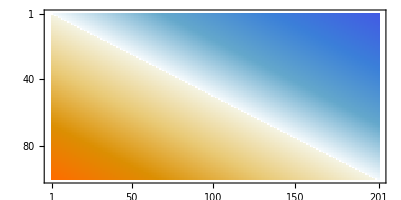

```mathematica
mPlot[100, 101.1]
```

```mathematica
mPlot [m_Integer, n_Real]=.
```

We can add more restriction using conditions.

```mathematica
mPlot [m_Integer, n_Real]:=MatrixPlot[Table[x-y, {x, 1, m}, {y, 1, n}]]/;(m>88 && m<99)||(n>88.8&&n<99.9)
```

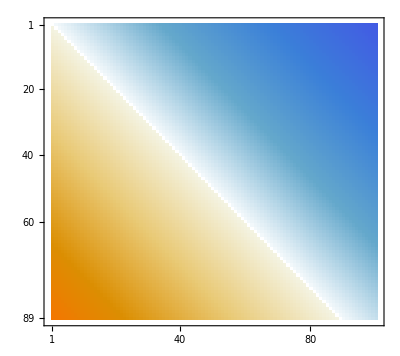

```mathematica
mPlot[89, 100.1]
```

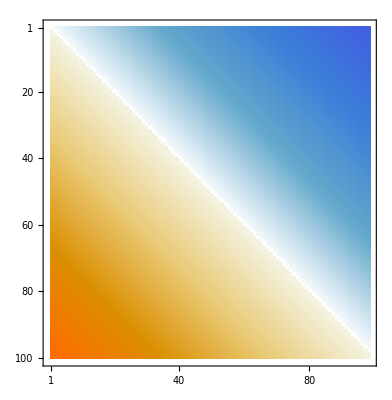

```mathematica
mPlot[100, 98.8]
```

```mathematica
mPlot[89,89]
```

mPlot[89,89]

```mathematica
Clear[mPlot]
```

```mathematica
mPlot [m_Integer, n_Real]:=MatrixPlot[Table[x-y, {x, 1, m}, {y, 1, n, 0.5}]]/;m≠99
```

```mathematica
mPlot[99, 101.1]
```

mPlot[99,101.1]

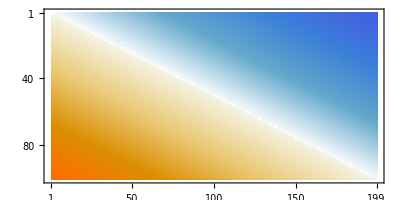

```mathematica
mPlot[100, 100.1]
```

## v. Define a function by incorporating a built-in ‘Check’ function, restricting the type of the input expression, and using the If conditions.

We can also use a Q built-in function (Query) in the Wolfram Language to find out the True/False, including it in the self-defined function.

```mathematica
pdq[n_String]:=If [PalindromeQ[n]==True,Print["You have got it right!"], Print["No! Try a different string."]]
```

```mathematica
pdq[x33x]
```

pdq[x33x]

```mathematica
pdq[1221]
```

pdq[1221]

```mathematica
pdq["Pooh Bear"]
```

No! Try a different string.

```mathematica
pdq["112211"]
```

You have got it right!

```mathematica
pdq["abba"]
```

You have got it right!

```mathematica
Clear[pdq]
```

The Wolfram Language has a large number of built-in functions to make query of input data for validation. Though we do not have time for this session to look into query functions, it is worth knowing that they exist.

Question: how do we know how many different built-in functions are available to enquire and validate data? Hint: this type of function usually takes the form of the head of ‘xxxQ[ ]’.

```mathematica
?*Q
```

## Exercise: 1. Write a self-defined function to convert from Fahrenheit to Celsius 2. Call the temperature converter function to see if the conversion works. 3. Use ThermormeterGauge[ ] to show the Celsius, converted from Fahrenheit 85 degrees, with the thermometer scale going from 0 to 100. Use the online documentation to find out how to use ThermormeterGauge.

## Answers:

```mathematica
tempConverter[f_]:=N[(f-32)*5/9]
```

```mathematica
tempConverter[85]
```

29.4444

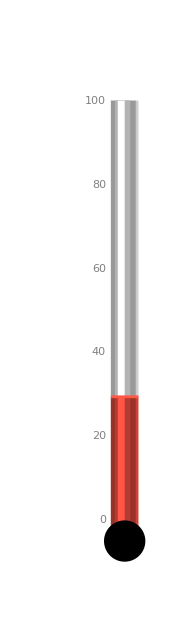

```mathematica
ThermometerGauge[tempConverter[85], {0, 100}]
```

## Part 8: More on Data/File Import and Export

Mathematica handles a large number of various data types. In this section we are going to see how to import data.

1. Supported imported/exported data/file type by the Wolfram Language?

```mathematica
$ImportFormats
```

{3DS,ACO,Affymetrix,AgilentMicroarray,AIFF,ApacheLog,ArcGRID,AU,AVI,Base64,BDF,Binary,Bit,BMP,BSON,Byte,BYU,BZIP2,CDED,CDF,Character16,Character8,CIF,Complex128,Complex256,Complex64,CSV,CUR,DAE,DBF,DICOM,DIF,DIMACS,Directory,DOT,DXF,EDF,EML,EPS,ExpressionJSON,ExpressionML,FASTA,FASTQ,FCS,FITS,FLAC,GenBank,GeoJSON,GeoTIFF,GIF,GPX,Graph6,Graphlet,GraphML,GRIB,GTOPO30,GXL,GZIP,HarwellBoeing,HDF,HDF5,HIN,HTML,HTTPRequest,HTTPResponse,ICC,ICNS,ICO,ICS,Ini,Integer128,Integer16,Integer24,Integer32,Integer64,Integer8,JavaProperties,JavaScriptExpression,JCAMP-DX,JPEG,JPEG2000,JSON,JVX,KML,LaTeX,LEDA,List,LWO,MAT,MathML,MBOX,MCTT,MDB,MESH,MGF,MIDI,MMCIF,MO,MOL,MOL2,MP3,MPS,MTP,MTX,MX,MXNet,NASACDF,NB,NDK,NetCDF,NEXUS,NOFF,OBJ,ODS,OFF,OGG,OpenEXR,Package,Pajek,PBM,PCAP,PCX,PDB,PDF,PGM,PHPIni,PLY,PNG,PNM,PPM,PXR,PythonExpression,QuickTime,Raw,RawBitmap,RawJSON,Real128,Real32,Real64,RIB,RLE,RSS,RTF,SCT,SDF,SDTS,SDTSDEM,SFF,SHP,SMA,SME,SMILES,SND,SP3,Sparse6,STL,String,SurferGrid,SXC,Table,TAR,TerminatedString,TeX,Text,TGA,TGF,TIFF,TIGER,TLE,TSV,UBJSON,UnsignedInteger128,UnsignedInteger16,UnsignedInteger24,UnsignedInteger32,UnsignedInteger64,UnsignedInteger8,USGSDEM,UUE,VCF,VCS,VTK,WARC,WAV,Wave64,WDX,WebP,WLNet,WMLF,WXF,XBM,XHTML,XHTMLMathML,XLS,XLSX,XML,XPORT,XYZ,ZIP}

```mathematica
$ExportFormats
```

{3DS,ACO,AIFF,AU,AVI,Base64,Binary,Bit,BMP,BSON,Byte,BYU,BZIP2,C,CDF,Character16,Character8,Complex128,Complex256,Complex64,CSV,CUR,DAE,DICOM,DIF,DIMACS,DOT,DXF,EMF,EPS,ExpressionJSON,ExpressionML,FASTA,FASTQ,FCS,FITS,FLAC,FLV,FMU,GeoJSON,GIF,Graph6,Graphlet,GraphML,GXL,GZIP,HarwellBoeing,HDF,HDF5,HTML,HTMLFragment,HTTPRequest,HTTPResponse,ICNS,ICO,Ini,Integer128,Integer16,Integer24,Integer32,Integer64,Integer8,JavaProperties,JavaScriptExpression,JPEG,JPEG2000,JSON,JVX,KML,LEDA,List,LWO,MAT,MathML,Maya,MCTT,MGF,MIDI,MO,MOL,MOL2,MP3,MTX,MX,MXNet,NASACDF,NB,NetCDF,NEXUS,NOFF,OBJ,OFF,OGG,Package,Pajek,PBM,PCX,PDB,PDF,PGM,PHPIni,PLY,PNG,PNM,POV,PPM,PXR,PythonExpression,RawBitmap,RawJSON,Real128,Real32,Real64,RIB,RTF,SCT,SDF,SMA,SND,Sparse6,STL,String,SurferGrid,SVG,SWF,Table,TAR,TerminatedString,TeX,TeXFragment,Text,TGA,TGF,TIFF,TSV,UBJSON,UnsignedInteger128,UnsignedInteger16,UnsignedInteger24,UnsignedInteger32,UnsignedInteger64,UnsignedInteger8,UUE,VideoFrames,VRML,VTK,WAV,Wave64,WDX,WebP,WLNet,WMLF,WXF,X3D,XBM,XHTML,XHTMLMathML,XLS,XLSX,XML,XYZ,ZIP,ZPR}

2. Data/file import?

## i. Import data/file locally:

We can use File Browser or specify the file path with double quotes wrapping around the path

```mathematica
Import["/home/Pooh_Centos/Desktop/MTM_Revised/model.dae"]
```

-Graphics3D-

Model source: <https://3dwarehouse.sketchup.com/model/38886365-99fb-4356-b023-80a431ac2ed1/Skill-Builder-Follow-Me-Arc>

We can use Directory to enquire the current working directory to find out the folder in which the working notebook is saved.

```mathematica
Directory[]
```

/home/Pooh_Centos/Desktop/IntroMM_Jan2019

We can set the Directory to a different folder, use Directory[ ] again to see if the setting has taken effect.

Once the working directory is set, we can make it much easier to make query of the files in the set directory.

```mathematica
FileNames[]
```

{.git,LazyPanda.jpg,MathematicaTeachingMaterial_FullVersion02.nb,MM1_5.nb,MM6_9.nb,model.dae,README.md,ScriptLoad.wls,SerialKiller_byCountry.csv,SerialKiller_byYear.csv,SerialKillerVictims_byAge.csv,TestPackage.m}

We use Import[ ] to import the file directly into the notebook.

```mathematica
Import["LazyPanda.jpg"]
```

-Graphics-

Alternatively, we use SystemOpen[ ] to have the file shown by using the defaulted software package on your system.

```mathematica
SystemOpen["LazyPanda.jpg"]
```

## ii. Import data/file from an accessible URL or FTP address:

We have already practiced this when we used the image of a lazy panda previously. Let’s use the example again:

```mathematica
pandaPhoto=Import["https://www.pandasinternational.org/wptemp/wp-content/uploads/2012/10/slider1.jpg"]
```

-Graphics-

```mathematica
Import["https://reference.wolfram.com/language/ref/ParametricPlot3D.html", "Images"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
chikaDetsu=StringTake[Import["https://ja.wikipedia.org/wiki/%E9%83%BD%E5%96%B6%E5%9C%B0%E4%B8%8B%E9%89%84", "HTML"], 300]
```

都営地下鉄  
 
出典: フリー百科事典『ウィキペディア（Wikipedia）』  
 
  ナビゲーションに移動   検索に移動  

地下鉄 > 日本の地下鉄 > 東京都内の地下鉄 > 都営地下鉄  
 
   「 東京地下鉄 」あるいは「 東京都電車 」とは異なります。     
都営地下鉄
  
1989年6月1日に制定された
東京都のシンボルマークを使用（局章は別に制定）。
基本情報
国    日本
所在地   東京都 、 千葉県 市川市
種類   地下鉄
開業  1960年12月4日
運営者   東京都交通局
公式サイト   都営地下鉄公式ウェブサイト
詳細情報
総延長距離  1

## iii. Load data from the example data the Mathematica software package provides (unfortunately not always works ):

```mathematica
ExampleData[]
```

{AerialImage,Audio,ColorTexture,Dataset,Geometry3D,LinearProgramming,MachineLearning,Matrix,NetworkGraph,Sound,Statistics,TestAnimation,TestImage,TestImage3D,TestImageSet,Text,Texture}

```mathematica
ExampleData["Geometry3D"]
```

{{Geometry3D,BassGuitar},{Geometry3D,Beethoven},{Geometry3D,CastleWall},{Geometry3D,Cone},{Geometry3D,Cow},{Geometry3D,Deimos},{Geometry3D,Galleon},{Geometry3D,HammerheadShark},{Geometry3D,Horse},{Geometry3D,KleinBottle},{Geometry3D,MoebiusStrip},{Geometry3D,Phobos},{Geometry3D,PottedPlant},{Geometry3D,Seashell},{Geometry3D,SedanCar},{Geometry3D,SpaceShuttle},{Geometry3D,StanfordBunny},{Geometry3D,Torus},{Geometry3D,Tree},{Geometry3D,Triceratops},{Geometry3D,Tugboat},{Geometry3D,UtahTeapot},{Geometry3D,UtahVWBug},{Geometry3D,Vase},{Geometry3D,VikingLander},{Geometry3D,Wrench},{Geometry3D,Zeppelin}}

```mathematica
ExampleData[{"Geometry3D","VikingLander"}]
```

-Graphics3D-

```mathematica
ExampleData["Dataset"]
```

{{Dataset,Planets},{Dataset,StatePopulations},{Dataset,Titanic}}

```mathematica
population=ExampleData[{"Dataset", "StatePopulations"}]
```

Dataset[<>]

```mathematica
Dimensions[population]
```

{198}

## iv. Load Script Files (.wls):

### <1>. What is a script file?

“A Wolfram Language script is simply a file containing Wolfram Language commands that you would normally evaluate sequentially in a Wolfram Language session. Writing a script is useful if the commands need to be repeated many times. Collecting these commands together ensures that they are evaluated in a particular sequence with no command omitted. This is important if you run complex and long calculations.”
(reference: https://reference.wolfram.com/language/tutorial/WolframLanguageScripts.html)

Note: Starting from Mathematica 11.1.0, the Wolfram Language starts with a WolframScript function, which takes the file extension name of ‘.wls’. Any version prior to 11.1.0 does not give the file extension name option ‘.wls’ in the drop-down menu to users when they go for -> Save As. Instead, only ‘.wl’ option is available, which is for the Wolfram Language Package in the Wolfram Language’s convention.

### <2>. How to create a script file?

<a>. Not using Mathematica notebook: Open a text editor (no Microsoft Office). For windows users, it is recommended that you use notepad++. Save the file with the extension name of .wl or .wls.
<b>. Using Mathematica notebook: (At the top ribbon) File-->New-->Script (.wls). For version prior to 11.1.0, go for File-->New-->Package (.wl)

Now let’s create a script file using the following set of code. You can copy and paste into the .wl or .wls file. Name it anything you like. For this session, I name it ScriptTest.wls.

data = RandomVariate[MultivariatePoissonDistribution[1, {3, 6}], 1000];
plotting=Histogram3D[data, 20, “ProbabilityDensity”];
Print[plotting]

### <3>. How to run a script file?

<a>. open the file manually from the top-ribbon menu, File->Open.

<b>. use Get[ ] command (or “<<”):

Now make sure that the script file is saved in the default folder. If you do not remember the default folder, use Directory[ ] to enquire.

Let’s use the built-in function Get[ ] to load the script.

```mathematica
Directory[]
```

/home/Pooh_Centos/Desktop/IntroMM_Jan2019

```mathematica
Get["ScriptLoad.wls"]
```

-Graphics3D-

```mathematica
<<ScriptLoad.wls
```

-Graphics3D-

## v. Load Packages (.m):

### <1>. What is a package?

“A Mathematica package is used to store Mathematica code so that it can be loaded into a Mathematica session, and it usually provides one or more functions to suit the specific need of users in a particular specialized area. The functions defined in a package are placed into a context or group of Mathematica symbols. The code that gives the functionality is hidden in an implementation section of the package.”

### <2>. How to create a package?

<a>. Not using Mathematica notebook: Open a text editor (no Microsoft Office). For windows users, it is recommended that you use notepad++. Save the file with the extension name of .m.
<b>. Using Mathematica notebook: (At the top ribbon) File-->New-->Script (.wls). Remember to always save the file as .m.

Here is a template of package creation:

BeginPackage[“NameofPackage`”]
             
             public-functions-usage-messages (this is where documentation goes to let users know what functionality has been defined and what the functionality does)

Begin[“`Private`”]

            code (this is the implementation of the set of code, which is hidden)

End[ ]

EndPackage[ ]

Let’s write a simple package of calculating a*b.

### <3>. How to run a package?

```mathematica
SetDirectory ["/home/Pooh_Centos/Desktop/MTM_Revised"]
```

/home/Pooh_Centos/Desktop/MTM_Revised

```mathematica
FileNames[ ]
```

{.git,LazyPanda.jpg,MathematicaTeachingMaterial_FullVersion01.nb,MathematicaTeachingMaterial.nb,MathematicaTeachingMaterial_Revised.nb,MathematicaTeachingMaterial_Skeleton.nb,mbTableView.csv,MM_Skeleton.nb,model.dae,Not_in_Use,PackageHowto.nb,ScriptLoad.wls,SerialKiller_byCountry_2018.csv,SerialKiller_byYear.csv,SerialKiller_Data.xlsx,SerialKillerVictims_byAge.csv,ShortVersion1_5.nb,ShortVersion6_9.nb,TestPackage.m,TextPictures}

```mathematica
<<TestPackage.m
```

```mathematica
$Packages
```

{testPackage`,GIFTools`,GeometryTools`,Dataset`,XMPTools`,TypeSystem`,WikipediaData`,WikipediaFunctions`,DataDropClient`,Interpreter`,ChannelFramework`,Developer`,QuantityUnits`,CloudObject`UserManagement`,CloudObject`,MailReceiver`,GeneralUtilities`,Templating`,Authentication`,Iconize`,UUID`,Security`,SVTools`,Utilities`URLTools`,DocumentationSearch`,CURLLink`URLResponseTime`,CURLLink`Utilities`,CURLInfo`,CURLLink`Cookies`,CURLLink`HTTP`,OAuthSigning`,CURLLink`URLFetch`,CURLLink`,WolframAlphaClient`,Macros`,DocumentationSearch`Skeletonizer`,JLink`,GetFEKernelInit`,JSONTools`,URLUtilities`,CloudPublishMenu`,CloudObjectLoader`,ExternalEvaluateLoader`,NeuralNetworks`,WolframBlockchain`,NeuralFunctions`,MobileMessaging`,IntegratedServices`,IconizeLoader`,HTTPHandling`,Forms`,SystemTools`,MailLinkLoader`,IMAPLinkLoader`,ResourceLocator`,PacletManager`,PersistenceLocations`,System`,Global`}

```mathematica
Import["TestPackage.m", "Elements"]
```

{Comments,ExpressionList,HeldExpressions,InactivatedExpressions}

```mathematica
Import["TestPackage.m","Comments"]
```

{::Package::,::This is a test package::}

```mathematica
Import["TestPackage.m", "Rules"]
```

{Comments→{::Package::,::This is a test package::},ExpressionList→{Null,Null,Null,Null,Null,Null},HeldExpressions→{HoldComplete[BeginPackage[testPackage`];],HoldComplete[timesTwo::usage=timesTwo[a, b], return a*b;],HoldComplete[Begin[`Private`];],HoldComplete[timesTwo[a_,b_]:=a b;],HoldComplete[End[];],HoldComplete[EndPackage[];]},InactivatedExpressions→{BeginPackage[testPackage`];,MessageName[timesTwo,usage]=timesTwo[a, b], return a*b;,Begin[`Private`];,timesTwo[a_,b_]:=a*b;,End[];,EndPackage[];}}

```mathematica
Import["TestPackage.m", "InactivatedExpressions"]
```

{BeginPackage[testPackage`];,MessageName[timesTwo,usage]=timesTwo[a, b], return a*b;,Begin[`Private`];,timesTwo[a_,b_]:=a*b;,End[];,EndPackage[];}

```mathematica
timesTwo[56.889, 334.112]
```

19007.3

## Part 9: A Revisit of Getting Help and Useful Resources:

1. Getting help:

i. ? to enquire the functionality of Functions.
ii. Drop-down option for Head (build-in functions and self-defined functions) and Wild card.
iii. Help ribbon or F1 for Wolfram Documentation. 
iv. Palettes ribbon for typesetting and calculator functionality.
v. Suggestion bar after evaluation.
vi. Free-form input and Wolfram Alpha Online Query for human-language query:

2. Resources:

i. http://www.wolfram.com/language/elementary-introduction/2nd-ed/; http://www.wolfram.com/wolfram-u/an-elementary-introduction-to-the-wolfram-language/ (An Elementary Introduction to Wolfram Language, 2nd Edition)
ii. http://www.wolfram.com/language/fast-introduction-for-programmers/en/ (Fast introduction for Programmers)
iii. http://www.wolfram.com/wolfram-u/ (Open courses for students and professionals)
     -Graphics-
iv. https://datarepository.wolframcloud.com/?source=nav (a public resource which hosts an expanding collection of computable datasets, curated and structured to be computed and analyzed).
-Graphics-
v. http://demonstrations.wolfram.com/ (an expanding repository which hosts various demo projects. All codes are public and downloadable for you to tweak them to suit your need).
-Graphics-	
vi. http://community.wolfram.com/?source=nav (discussion forum)
vii. https://mathematica.stackexchange.com/ (stackexchange for Mathematica related questions and discussions, in-depth discussion is raised there).
viii. functions.wlfram.com (The Wolfram Functions Site: claiming to be the world’s largest collection of formulas and graphics about mathematical functions).

-Graphics-
viv. mathworld.wolfram.com (claiming to the web’s most extensive mathematics resource)

-Graphics-